```mathematica
(* ============================================ UTILITY FUNCTIONS =========================================*)ExtractQubitLabelsArray[Nqubits_,index_]:=2 IntegerDigits[index-1,2,Nqubits]-1
ComputeTildeRJ[Nqubits_,Jlabels_,Hminv_,rhamArray_]:=FullSimplify[Hminv.(rhamArray[[1]]+Sum[Jlabels[[i]] rhamArray[[i+1]],{i,1,Nqubits}])]
SymplecticMatrix[nmodes_]:=BlockDiagonalMatrix@Table[{{0,1},{-1,0}},{nmodes}]

(* ============================================= STATE CONSTRUCTOR ==========================================*)

QuantumState[Nqubits_,nmodes_,ρq_,σ_,RMatrixRe_,RMatrixIm_,CMatrix_,PhiMatrix_]:=<|"Nqubits"->Nqubits,"nmodes"->nmodes,"rhoq"->ρq,"Sigma"->σ,"RMatrixRe"->RMatrixRe,"RMatrixIm"->RMatrixIm,"CMatrix"->CMatrix,"PhiMatrix"->PhiMatrix|>

StateQ[s_]:=AssociationQ[s]&&ContainsAll[Keys[s],{"Nqubits","nmodes","rhoq","Sigma","RMatrixRe","RMatrixIm","CMatrix","PhiMatrix"}]


(* ================================================ DYNAMICS ================================================*) 

(* ================================================ UNITARY ================================================*) 

(* ========================= LOWEST LEVEL ========================*)

ComputeRJKReUnitaryForce[nmodes_,r0tRe_,rJt_,rJ_,rKt_,rK_]:=r0tRe-1/2 (rJt-rJ+rKt-rK)
ComputeRJKImUnitaryForce[nmodes_,r0tIm_,σt_,rJt_,rJ_,rKt_,rK_,Ω_]:=r0tIm-1/2 σt.Ω.(rJt-rJ-rKt+rK)
ComputeCJKUnitaryForce[nmodes_,σt_,r0tIm_,r0Im_,rJt_,rJ_,rKt_,rK_,Ω_]:=FullSimplify[1/4 Transpose[rJt-rJ-rKt+rK].Transpose[Ω].σt.Ω.(rJt-rJ-rKt+rK)+Transpose[rJ-rK].Ω.(r0tIm-r0Im)][[1,1]]
ComputePhiJKUnitaryForce[nmodes_,r0tRe_,r0Re_,rJt_,rJ_,rKt_,rK_,Hm_,Hq0Array_,Jlabels_,Klabels_,time_,Ω_]:=Module[{phi1,phi2,phi3},phi1=-Transpose[rJ-rK].Ω.(r0tRe-r0Re);
phi2=1/2 Transpose[rJ-rK].Ω.(rJt-rJ+rKt-rK);
phi3=time/2 (Transpose[rJ-rK].Hm.(rJ+rK)-Transpose[Hq0Array].(Jlabels-Klabels));
(phi1+phi2+phi3)[[1,1]]]

(* =========================== MID LEVEL ========================*)

ComputeRMatrixReUnitaryForce[Nqubits_,nmodes_,Sm_,Hminv_,rhamArray_,RMatrixRe_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,j],Hminv,rhamArray];
rK=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,k],Hminv,rhamArray];
FullSimplify@ComputeRJKReUnitaryForce[nmodes,Sm.RMatrixRe[[j,k]],Sm.rJ,rJ,Sm.rK,rK]]],{2^Nqubits,2^Nqubits}]
ComputeRMatrixImUnitaryForce[Nqubits_,nmodes_,Sm_,σt_,Hminv_,rhamArray_,RMatrixIm_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,j],Hminv,rhamArray];
rK=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,k],Hminv,rhamArray];
FullSimplify@ComputeRJKImUnitaryForce[nmodes,Sm.RMatrixIm[[j,k]],σt,Sm.rJ,rJ,Sm.rK,rK,Ω]]],{2^Nqubits,2^Nqubits}]
ComputeCMatrixUnitaryForce[Nqubits_,nmodes_,σt_,Sm_,Hminv_,rhamArray_,RMatrixIm_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,j],Hminv,rhamArray];
rK=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,k],Hminv,rhamArray];
ComputeCJKUnitaryForce[nmodes,σt,Sm.RMatrixIm[[j,k]],RMatrixIm[[j,k]],Sm.rJ,rJ,Sm.rK,rK,Ω]]],{2^Nqubits,2^Nqubits}]
ComputePhiMatrixUnitaryForce[Nqubits_,nmodes_,σt_,Sm_,Hminv_,rhamArray_,Hm_,Hq0Array_,time_,RMatrixRe_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,j],Hminv,rhamArray];
rK=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,k],Hminv,rhamArray];
FullSimplify@ComputePhiJKUnitaryForce[nmodes,Sm.RMatrixRe[[j,k]],RMatrixRe[[j,k]],Sm.rJ,rJ,Sm.rK,rK,Hm,Hq0Array,ExtractQubitLabelsArray[Nqubits,j],ExtractQubitLabelsArray[Nqubits,k],time,Ω]]],{2^Nqubits,2^Nqubits}]

(* ============================== TOP LEVEL ==============================*)

ComputeQRDM[Nqubits_,CMatrix_,PhiMatrix_,ρq0_]:=Array[Function[{j,k},ρq0[[j,k]]*E^(-CMatrix[[j,k]]+I PhiMatrix[[j,k]])],{2^Nqubits,2^Nqubits}]
EvolveQuantumState[s_?StateQ,Hm_,Hq0Array_,rhamArray_,time_]:=Module[{Ω,Sm,Hminv,σt,RnewRe,RnewIm,Cnew,Phinew,ρqnew},Ω=SymplecticMatrix[s["nmodes"]];
Sm=FullSimplify@MatrixExp[time Ω.Hm];
Hminv=FullSimplify@Inverse[Hm];
σt=FullSimplify[Sm.s["Sigma"].Transpose[Sm]];
RnewRe=ComputeRMatrixReUnitaryForce[s["Nqubits"],s["nmodes"],Sm,Hminv,rhamArray,s["RMatrixRe"],Ω];
RnewIm=ComputeRMatrixImUnitaryForce[s["Nqubits"],s["nmodes"],Sm,σt,Hminv,rhamArray,s["RMatrixIm"],Ω];
Cnew=FullSimplify@ComputeCMatrixUnitaryForce[s["Nqubits"],s["nmodes"],σt,Sm,Hminv,rhamArray,s["RMatrixIm"],Ω];
Phinew=FullSimplify@ComputePhiMatrixUnitaryForce[s["Nqubits"],s["nmodes"],σt,Sm,Hminv,rhamArray,Hm,Hq0Array,time,s["RMatrixRe"],Ω];
ρqnew=ComputeQRDM[s["Nqubits"],Cnew,Phinew,s["rhoq"]];
QuantumState[s["Nqubits"],s["nmodes"],ρqnew,σt,RnewRe,RnewIm,Cnew,Phinew]]

(* ================================================ DIFFIUSING OPEN ================================================*) 

(* ========================= LOWEST LEVEL ========================*)

LyapunovPropagator[tp_,Hm_,Ω_,time_]:=MatrixExp[Ω.Hm.(time-tp)]
ComputeSigmaOpenForce[σ0_,Sm_,Hm_,Dmat_,Ω_,time_]:=FullSimplify[Sm.σ0.Transpose[Sm]+Integrate[LyapunovPropagator[tp,Hm,Ω,time].Dmat.Transpose[LyapunovPropagator[tp,Hm,Ω,time]],{tp,0,time}]]
ComputeRJKReOpenForce[nmodes_,r0tRe_,rJt_,rJ_,rKt_,rK_]:=r0tRe-1/2 (rJt-rJ+rKt-rK)
ComputeRJKImOpenForce[nmodes_,r0tIm_,σt_,rJt_,rJ_,rKt_,rK_,Hm_,Dmat_,Ω_,time_]:=FullSimplify[r0tIm-1/2 σt.Ω.(rJt-rJ-rKt+rK)-1/2 Integrate[LyapunovPropagator[tp,Hm,Ω,time].Dmat.Transpose[LyapunovPropagator[tp,Hm,Ω,time]].Ω.((LyapunovPropagator[tp,Hm,Ω,time].rJ-rJt)-(LyapunovPropagator[tp,Hm,Ω,time].rK-rKt)),{tp,0,time}]]
ComputeCJKOpenForce[nmodes_,σt_,r0tIm_,r0Im_,rJt_,rJ_,rKt_,rK_,Hm_,Dmat_,Ω_,time_]:=FullSimplify[1/4 Transpose[rJt-rJ-rKt+rK].Transpose[Ω].σt.Ω.(rJt-rJ-rKt+rK)+Transpose[rJ-rK].Ω.(r0tIm-r0Im)+1/4 Integrate[Transpose[(LyapunovPropagator[tp,Hm,Ω,time].rJ-rJt)-(LyapunovPropagator[tp,Hm,Ω,time].rK-rKt)].Transpose[Ω].LyapunovPropagator[tp,Hm,Ω,time].Dmat.Transpose[LyapunovPropagator[tp,Hm,Ω,time]].Ω.((LyapunovPropagator[tp,Hm,Ω,time].rJ+rJt-2 rJ)-(LyapunovPropagator[tp,Hm,Ω,time].rK+rKt-2 rK)),{tp,0,time}]][[1,1]]
ComputePhiJKOpenForce[nmodes_,r0tRe_,r0Re_,rJt_,rJ_,rKt_,rK_,Hm_,Hq0Array_,Jlabels_,Klabels_,time_,Ω_]:=Module[{phi1,phi2,phi3},phi1=-Transpose[rJ-rK].Ω.(r0tRe-r0Re);
phi2=1/2 Transpose[rJ-rK].Ω.(rJt-rJ+rKt-rK);
phi3=time/2 (Transpose[rJ-rK].Hm.(rJ+rK)-Transpose[Hq0Array].(Jlabels-Klabels));
(phi1+phi2+phi3)[[1,1]]]

(* ========================= MID LEVEL ========================*)

ComputeRMatrixReOpenForce[Nqubits_,nmodes_,Sm_,Hminv_,rhamArray_,RMatrixRe_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,j],Hminv,rhamArray];
rK=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,k],Hminv,rhamArray];
FullSimplify@ComputeRJKReOpenForce[nmodes,Sm.RMatrixRe[[j,k]],Sm.rJ,rJ,Sm.rK,rK]]],{2^Nqubits,2^Nqubits}]
ComputeRMatrixImOpenForce[Nqubits_,nmodes_,Sm_,σt_,Hminv_,rhamArray_,RMatrixIm_,Hm_,Dmat_,Ω_,time_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,j],Hminv,rhamArray];
rK=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,k],Hminv,rhamArray];
ComputeRJKImOpenForce[nmodes,Sm.RMatrixIm[[j,k]],σt,Sm.rJ,rJ,Sm.rK,rK,Hm,Dmat,Ω,time]]],{2^Nqubits,2^Nqubits}]
ComputeCMatrixOpenForce[Nqubits_,nmodes_,σt_,Sm_,Hminv_,rhamArray_,RMatrixIm_,Hm_,Dmat_,Ω_,time_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,j],Hminv,rhamArray];
rK=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,k],Hminv,rhamArray];
ComputeCJKOpenForce[nmodes,σt,Sm.RMatrixIm[[j,k]],RMatrixIm[[j,k]],Sm.rJ,rJ,Sm.rK,rK,Hm,Dmat,Ω,time]]],{2^Nqubits,2^Nqubits}]
ComputePhiMatrixOpenForce[Nqubits_,nmodes_,σt_,Sm_,Hminv_,rhamArray_,Hm_,Hq0Array_,time_,RMatrixRe_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,j],Hminv,rhamArray];
rK=ComputeTildeRJ[Nqubits,ExtractQubitLabelsArray[Nqubits,k],Hminv,rhamArray];
FullSimplify@ComputePhiJKOpenForce[nmodes,Sm.RMatrixRe[[j,k]],RMatrixRe[[j,k]],Sm.rJ,rJ,Sm.rK,rK,Hm,Hq0Array,ExtractQubitLabelsArray[Nqubits,j],ExtractQubitLabelsArray[Nqubits,k],time,Ω]]],{2^Nqubits,2^Nqubits}]

(* ========================= TOP LEVEL ========================*)

EvolveQuantumStateOpen[s_?StateQ,Hm_,Hq0Array_,rhamArray_,Dmat_,time_]:=Module[{Ω,Sm,Hminv,σt,RnewRe,RnewIm,Cnew,Phinew,ρqnew},Ω=SymplecticMatrix[s["nmodes"]];
Sm=FullSimplify@MatrixExp[time Ω.Hm];
Hminv=FullSimplify@Inverse[Hm];
σt=ComputeSigmaOpenForce[s["Sigma"],Sm,Hm,Dmat,Ω,time];
RnewRe=ComputeRMatrixReOpenForce[s["Nqubits"],s["nmodes"],Sm,Hminv,rhamArray,s["RMatrixRe"],Ω];
RnewIm=ComputeRMatrixImOpenForce[s["Nqubits"],s["nmodes"],Sm,σt,Hminv,rhamArray,s["RMatrixIm"],Hm,Dmat,Ω,time];
Cnew=FullSimplify@ComputeCMatrixOpenForce[s["Nqubits"],s["nmodes"],σt,Sm,Hminv,rhamArray,s["RMatrixIm"],Hm,Dmat,Ω,time];
Phinew=FullSimplify@ComputePhiMatrixOpenForce[s["Nqubits"],s["nmodes"],σt,Sm,Hminv,rhamArray,Hm,Hq0Array,time,s["RMatrixRe"],Ω];
ρqnew=ComputeQRDM[s["Nqubits"],Cnew,Phinew,s["rhoq"]];
QuantumState[s["Nqubits"],s["nmodes"],ρqnew,σt,RnewRe,RnewIm,Cnew,Phinew]]


(* ============================================== OPERTATOR VALUED DISPLACEMENTS ================================================*) 

(* =================== LOWEST LEVEL ======================*)

ComputeRJKReDisplacement[nmodes_,rJKRe_,rJ_,rK_]:=rJKRe-1/2 (rJ+rK)
ComputeRJKImDisplacement[nmodes_,rJKIm_,σ_,rJ_,rK_,Ω_]:=rJKIm-1/2 σ.Ω.(rJ-rK)
ComputeCJKDisplacement[nmodes_,CJK_,rJKIm_,rJ_,rK_,σ_,Ω_]:=FullSimplify[CJK+1/4 Transpose[rJ-rK].Transpose[Ω].σ.Ω.(rJ-rK)+Transpose[rJ-rK].Ω.rJKIm][[1,1]]
ComputePhiJKDisplacement[nmodes_,PhiJK_,rJKRe_,rJ_,rK_,Ω_]:=FullSimplify[PhiJK+(Transpose[rJ-rK].Ω.rJKRe)[[1,1]]-1/2 (Transpose[rJ].Ω.rK)[[1,1]]]

(* =================== MID LEVEL ======================*)

ComputeRMatrixReDisplacement[Nqubits_,nmodes_,RMatrixRe_,rhamArray_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=rhamArray[[j]];
rK=rhamArray[[k]];
FullSimplify@ComputeRJKReDisplacement[nmodes,RMatrixRe[[j,k]],rJ,rK]]],{2^Nqubits,2^Nqubits}]
ComputeRMatrixImDisplacement[Nqubits_,nmodes_,RMatrixIm_,σ_,rhamArray_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=rhamArray[[j]];
rK=rhamArray[[k]];
FullSimplify@ComputeRJKImDisplacement[nmodes,RMatrixIm[[j,k]],σ,rJ,rK,Ω]]],{2^Nqubits,2^Nqubits}]
ComputeCMatrixDisplacement[Nqubits_,nmodes_,CMatrix_,RMatrixIm_,σ_,rhamArray_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=rhamArray[[j]];
rK=rhamArray[[k]];
ComputeCJKDisplacement[nmodes,CMatrix[[j,k]],RMatrixIm[[j,k]],rJ,rK,σ,Ω]]],{2^Nqubits,2^Nqubits}]
ComputePhiMatrixDisplacement[Nqubits_,nmodes_,PhiMatrix_,RMatrixRe_,rhamArray_,Ω_]:=Array[Function[{j,k},Module[{rJ,rK},rJ=rhamArray[[j]];
rK=rhamArray[[k]];
ComputePhiJKDisplacement[nmodes,PhiMatrix[[j,k]],RMatrixRe[[j,k]],rJ,rK,Ω]]],{2^Nqubits,2^Nqubits}]

(* =================== TOP LEVEL ======================*)

DisplacementUpdate[s_?StateQ,rhamArray_]:=Module[{Ω,RnewRe,RnewIm,Cnew,Phinew,ρqnew},Ω=SymplecticMatrix[s["nmodes"]];
RnewRe=ComputeRMatrixReDisplacement[s["Nqubits"],s["nmodes"],s["RMatrixRe"],rhamArray];
RnewIm=ComputeRMatrixImDisplacement[s["Nqubits"],s["nmodes"],s["RMatrixIm"],s["Sigma"],rhamArray,Ω];
Cnew=ComputeCMatrixDisplacement[s["Nqubits"],s["nmodes"],s["CMatrix"],s["RMatrixIm"],s["Sigma"],rhamArray,Ω];
Phinew=ComputePhiMatrixDisplacement[s["Nqubits"],s["nmodes"],s["PhiMatrix"],s["RMatrixRe"],rhamArray,Ω];
ρqnew=ComputeQRDM[s["Nqubits"],Cnew,Phinew,s["rhoq"]];
QuantumState[s["Nqubits"],s["nmodes"],ρqnew,s["Sigma"],RnewRe,RnewIm,Cnew,Phinew]]

(* ============================================== GAUSSIAN MAPS AND OPERATIONS ================================================*) 

(* =================== LOWEST LEVEL ======================*)

ComputeSigmaJKGaussianMap[σJK_,SX_,X_,Y_,Ω_]:=FullSimplify[SX.σJK.Transpose[SX]+Ω.Inverse[X].Y.Inverse[Transpose[X]].Transpose[Ω]]
ComputeRJKReGaussianMap[nmodes_,rJKRe_,rc_,SX_]:=FullSimplify[SX.rJKRe+rc]
ComputeRJKImGaussianMap[nmodes_,rJKIm_,SX_]:=FullSimplify[SX.rJKIm]
ComputeCJKGaussianMap[nmodes_,CJK_,X_]:=FullSimplify[CJK+Log[Abs[Det[X]]]]
ComputePhiJKGaussianMap[nmodes_,PhiJK_]:=PhiJK

(* =================== MID LEVEL ======================*)

ComputeSigmaGaussianMap[σ_,SX_,X_,Y_,Ω_]:=ComputeSigmaJKGaussianMap[σ,SX,X,Y,Ω]
ComputeRMatrixReGaussianMap[Nqubits_,nmodes_,RMatrixRe_,rc_,SX_]:=Array[Function[{j,k},ComputeRJKReGaussianMap[nmodes,RMatrixRe[[j,k]],rc,SX]],{2^Nqubits,2^Nqubits}]
ComputeRMatrixImGaussianMap[Nqubits_,nmodes_,RMatrixIm_,SX_]:=Array[Function[{j,k},ComputeRJKImGaussianMap[nmodes,RMatrixIm[[j,k]],SX]],{2^Nqubits,2^Nqubits}]
ComputeCMatrixGaussianMap[Nqubits_,nmodes_,CMatrix_,X_]:=Array[Function[{j,k},ComputeCJKGaussianMap[nmodes,CMatrix[[j,k]],X]],{2^Nqubits,2^Nqubits}]
ComputePhiMatrixGaussianMap[Nqubits_,nmodes_,PhiMatrix_]:=PhiMatrix

(* =================== TOP LEVEL ======================*)

GaussianMapUpdate[s_?StateQ,X_,Y_,rc_]:=Module[{Ω,SX,σnew,RnewRe,RnewIm,Cnew,Phinew,ρqnew},Ω=SymplecticMatrix[s["nmodes"]];
SX=FullSimplify[Ω.Inverse[Transpose[X]].Transpose[Ω]];
σnew=ComputeSigmaGaussianMap[s["Sigma"],SX,X,Y,Ω];
RnewRe=ComputeRMatrixReGaussianMap[s["Nqubits"],s["nmodes"],s["RMatrixRe"],rc,SX];
RnewIm=ComputeRMatrixImGaussianMap[s["Nqubits"],s["nmodes"],s["RMatrixIm"],SX];
Cnew=ComputeCMatrixGaussianMap[s["Nqubits"],s["nmodes"],s["CMatrix"],X];
Phinew=ComputePhiMatrixGaussianMap[s["Nqubits"],s["nmodes"],s["PhiMatrix"]];
ρqnew=ComputeQRDM[s["Nqubits"],Cnew,Phinew,s["rhoq"]];
QuantumState[s["Nqubits"],s["nmodes"],ρqnew,σnew,RnewRe,RnewIm,Cnew,Phinew]]

(* ============================================== PLOTTING FUNCTIONS ================================================*) 

(* ============================================== FIRST MOMENTS TIME EVOLUTION ================================================*) 

PlotRMatrixEvolution[state_?StateQ,tVar_,tRange_,subs_,Nqubits_,nmodes_]:=Module[{tmin,tmax,dim,allPlots,plotSize},{tmin,tmax}=tRange;
dim=2^Nqubits;
plotSize=300;
allPlots=Table[Module[{compIdx1,diagPlot,offPlot},compIdx1=2 m-1;
(*----PLOT 1:Diagonal RMatrixRe[[i,i]]----*)diagPlot=Plot[Evaluate@Table[(state["RMatrixRe"][[i,i]]/. subs)[[compIdx1,1]]/. tVar->t,{i,1,dim}],{t,tmin,tmax},PlotStyle->Automatic,PlotLegends->Placed[Table[Row[{Subscript["r",Row[{i,i}]]," Re"}],{i,1,dim}],{Right,Top}],Frame->True,GridLines->Automatic,FrameLabel->{"t",Row[{"Mode ",m,": diag ",Subscript["r","jj"]}]},PlotLabel->Row[{"Mode ",m," — Diagonal RMatrixRe"}],ImageSize->{plotSize,plotSize},ImagePadding->{{50,10},{40,30}}];
(*----PLOT 2:Upper triangle Re (solid) and Im (dashed)----*)offPlot=Plot[Evaluate@Flatten[{Table[If[i<j,(state["RMatrixRe"][[i,j]]/. subs)[[compIdx1,1]]/. tVar->t,Nothing],{i,1,dim},{j,1,dim}],Table[If[i<j,(state["RMatrixIm"][[i,j]]/. subs)[[compIdx1,1]]/. tVar->t,Nothing],{i,1,dim},{j,1,dim}]}],{t,tmin,tmax},PlotStyle->Flatten[{Table[If[i<j,Directive[ColorData[97][i+j],Solid],Nothing],{i,1,dim},{j,1,dim}],Table[If[i<j,Directive[ColorData[97][i+j],Dashed],Nothing],{i,1,dim},{j,1,dim}]}],PlotLegends->Placed[Flatten[{Table[If[i<j,Row[{Subscript["r",Row[{i,j}]]," Re"}],Nothing],{i,1,dim},{j,1,dim}],Table[If[i<j,Row[{Subscript["r",Row[{i,j}]]," Im"}],Nothing],{i,1,dim},{j,1,dim}]}],{Right,Top}],Frame->True,GridLines->Automatic,FrameLabel->{"t",Row[{"Mode ",m,": off-diag ",Subscript["r","jk"]}]},PlotLabel->Row[{"Mode ",m," — Complex Off-diagonal"}],ImageSize->{plotSize,plotSize},ImagePadding->{{50,10},{40,30}}];
{diagPlot,offPlot}],{m,1,nmodes}];
GraphicsGrid[Partition[Flatten[allPlots],2],ImageSize->{2 plotSize,nmodes plotSize},Spacings->{0.2,0.2},PlotLabel->Style["First moments",Bold,16]]]

(* ================================================================WIGNER FUNCTION ================================================================*)

(*Extract 2x2 block for modeChosen from a 2nmodes x 2nmodes matrix*)ExtractModeBlock[mat_,modeChosen_]:=mat[[{2 modeChosen-1,2 modeChosen},{2 modeChosen-1,2 modeChosen}]]

(*Extract 2-vector block for modeChosen from a 2nmodes column vector*)
ExtractModeVec[vec_,modeChosen_]:=vec[[{2 modeChosen-1,2 modeChosen},{1}]]

(* ====================== GAUSSIAN TERM W_jj =============================================*)

WignerDiagonal[rvar_,ρjj_,σjj_,rjj_]:=Module[{σinv,dr},σinv=Inverse[σjj];
dr=rvar-rjj;
(2 ρjj)/(Pi Sqrt[Det[σjj]])*Exp[-(Transpose[dr].σinv.dr)[[1,1]]]]

(* ======================INTERFERENCE TERM W_f=2 Re[W_{12}]==========================================*)

WignerInterference[rvar_,ρ12_,σ_,rRe_,rIm_,Cjk_,ϕjk_]:=Module[{σinv,Σ,R,b,ϕ,𝒩},σinv=Inverse[σ];
Σ=σinv;
R=rRe;
b=σinv.rIm;
ϕ=-2 (Transpose[rIm].σinv.rRe)[[1,1]]+ϕjk;
𝒩=2 Abs[ρ12]*Exp[-Cjk+(Transpose[rIm].σinv.rIm)[[1,1]]]/(Pi Sqrt[Det[σ]]);
𝒩*Exp[-(Transpose[rvar-R].Σ.(rvar-R))[[1,1]]]*Sin[(Transpose[b].rvar)[[1,1]]+ϕ]]

(* =============================MAIN PLOTTING FUNCTION============================================*)

PlotWignerFunction[state_?StateQ,subs_,modeChosen_,xRange_:{-5,5},pRange_:{-5,5},plotSize_:300]:=Module[{σmInv,detSigma,a11,a12,a22,r11x,r11p,r22x,r22p,r12Rex,r12Rep,r12Imx,r12Imp,bx,bp,ϕtot,𝒩,rho11,rho22,rho12abs,fDiag,fInterf,fTotal,wMax,colorFunc,plotDiag,plotInterf,plotTotal,colorBar},σmInv=Inverse[ExtractModeBlock[state["Sigma"]/. subs//N,modeChosen]];
detSigma=1/Det[σmInv];
a11=σmInv[[1,1]];
a12=σmInv[[1,2]];
a22=σmInv[[2,2]];
r11x=(state["RMatrixRe"][[1,1]]/. subs//N)[[2 modeChosen-1,1]];
r11p=(state["RMatrixRe"][[1,1]]/. subs//N)[[2 modeChosen,1]];
r22x=(state["RMatrixRe"][[2,2]]/. subs//N)[[2 modeChosen-1,1]];
r22p=(state["RMatrixRe"][[2,2]]/. subs//N)[[2 modeChosen,1]];
r12Rex=(state["RMatrixRe"][[1,2]]/. subs//N)[[2 modeChosen-1,1]];
r12Rep=(state["RMatrixRe"][[1,2]]/. subs//N)[[2 modeChosen,1]];
r12Imx=(state["RMatrixIm"][[1,2]]/. subs//N)[[2 modeChosen-1,1]];
r12Imp=(state["RMatrixIm"][[1,2]]/. subs//N)[[2 modeChosen,1]];
rho11=Re[state["rhoq"][[1,1]]/. subs//N];
rho22=Re[state["rhoq"][[2,2]]/. subs//N];
rho12abs=Abs[state["rhoq"][[1,2]]/. subs//N];
bx=a11 r12Imx+a12 r12Imp;
bp=a12 r12Imx+a22 r12Imp;
ϕtot=-2 (r12Imx (a11 r12Rex+a12 r12Rep)+r12Imp (a12 r12Rex+a22 r12Rep))+(state["PhiMatrix"][[1,2]]/. subs//N);
𝒩=2 rho12abs*Exp[-(state["CMatrix"][[1,2]]/. subs//N)+r12Imx (a11 r12Imx+a12 r12Imp)+r12Imp (a12 r12Imx+a22 r12Imp)]/(Pi Sqrt[detSigma]);
fDiag=Compile[{{x,_Real},{p,_Real}},(2 rho11)/(Pi Sqrt[detSigma])*Exp[-(a11(x-r11x)^2+2 a12(x-r11x)(p-r11p)+a22(p-r11p)^2)]+(2 rho22)/(Pi Sqrt[detSigma])*Exp[-(a11(x-r22x)^2+2 a12(x-r22x)(p-r22p)+a22(p-r22p)^2)],{{rho11,_Real},{rho22,_Real},{detSigma,_Real},{a11,_Real},{a12,_Real},{a22,_Real},{r11x,_Real},{r11p,_Real},{r22x,_Real},{r22p,_Real}}];
fInterf=Compile[{{x,_Real},{p,_Real}},𝒩*Exp[-(a11(x-r12Rex)^2+2 a12(x-r12Rex)(p-r12Rep)+a22(p-r12Rep)^2)]*Sin[bx x+bp p+ϕtot],{{𝒩,_Real},{a11,_Real},{a12,_Real},{a22,_Real},{r12Rex,_Real},{r12Rep,_Real},{bx,_Real},{bp,_Real},{ϕtot,_Real}}];
fTotal=Compile[{{x,_Real},{p,_Real}},(2 rho11)/(Pi Sqrt[detSigma])*Exp[-(a11(x-r11x)^2+2 a12(x-r11x)(p-r11p)+a22(p-r11p)^2)]+(2 rho22)/(Pi Sqrt[detSigma])*Exp[-(a11(x-r22x)^2+2 a12(x-r22x)(p-r22p)+a22(p-r22p)^2)]+𝒩*Exp[-(a11(x-r12Rex)^2+2 a12(x-r12Rex)(p-r12Rep)+a22(p-r12Rep)^2)]*Sin[bx x+bp p+ϕtot],{{rho11,_Real},{rho22,_Real},{detSigma,_Real},{a11,_Real},{a12,_Real},{a22,_Real},{r11x,_Real},{r11p,_Real},{r22x,_Real},{r22p,_Real},{𝒩,_Real},{r12Rex,_Real},{r12Rep,_Real},{bx,_Real},{bp,_Real},{ϕtot,_Real}}];
(*----Compute symmetric color range from max of diagonal----*)wMax=Max[Table[fDiag[x,p],{x,xRange[[1]],xRange[[2]],(xRange[[2]]-xRange[[1]])/50.},{p,pRange[[1]],pRange[[2]],(pRange[[2]]-pRange[[1]])/50.}]];
(*----Symmetric diverging colormap:red-white-blue----*)(*t in[0,1]:0=most negative (red),0.5=zero (white),1=most positive (blue)*)colorFunc=Function[t,If[t<0.5,Blend[{RGBColor[0.8,0,0],White},2 t],Blend[{White,RGBColor[0,0,0.8]},2 t-1]]];
(*----Shared plot options----*)(*PlotRange symmetric,ColorFunctionScaling False so we map manually*)plotDiag=DensityPlot[fDiag[x,p],{x,xRange[[1]],xRange[[2]]},{p,pRange[[1]],pRange[[2]]},PlotRange->{-wMax,wMax},ColorFunction->(colorFunc[(#+wMax)/(2 wMax)]&),ColorFunctionScaling->False,Frame->True,FrameLabel->{{"p",None},{"x",None}},PlotLabel->Style["Diagonal 𝒲",Bold],ImageSize->{plotSize,plotSize},ImagePadding->{{50,10},{40,30}},PlotPoints->50,MaxRecursion->3];
plotInterf=DensityPlot[fInterf[x,p],{x,xRange[[1]],xRange[[2]]},{p,pRange[[1]],pRange[[2]]},PlotRange->{-wMax,wMax},ColorFunction->(colorFunc[(#+wMax)/(2 wMax)]&),ColorFunctionScaling->False,Frame->True,FrameLabel->{{"p",None},{"x",None}},PlotLabel->Style["Interference 𝒲",Bold],ImageSize->{plotSize,plotSize},ImagePadding->{{50,10},{40,30}},PlotPoints->50,MaxRecursion->3];
plotTotal=DensityPlot[fTotal[x,p],{x,xRange[[1]],xRange[[2]]},{p,pRange[[1]],pRange[[2]]},PlotRange->{-wMax,wMax},ColorFunction->(colorFunc[(#+wMax)/(2 wMax)]&),ColorFunctionScaling->False,Frame->True,FrameLabel->{{"p",None},{"x",None}},PlotLabel->Style["Total 𝒲",Bold],ImageSize->{plotSize,plotSize},ImagePadding->{{50,10},{40,30}},PlotPoints->50,MaxRecursion->3];
(*----Build standalone colorbar----*)colorBar=DensityPlot[y,{x,0,1},{y,-wMax,wMax},PlotRange->{-wMax,wMax},ColorFunction->(colorFunc[(#+wMax)/(2 wMax)]&),ColorFunctionScaling->False,Frame->True,FrameTicks->{{None,Table[{v,NumberForm[v,{3,2}]},{v,-wMax,wMax,2 wMax/4}]},{None,None}},FrameLabel->{{None,Style["𝒲",Italic]},{None,None}},FrameTicksStyle->Directive[Black,10],ImageSize->{70,plotSize},ImagePadding->{{0,45},{40,30}},AspectRatio->Full];
(*----Assemble final layout----*)Row[{GraphicsGrid[{{plotDiag,plotInterf,plotTotal}},Spacings->{0.2,0.2},ImageSize->{3 plotSize,plotSize},PlotLabel->Style[Row[{"Wigner Function — Mode ",modeChosen}],Bold,16]],colorBar}]]
```

## Atom-Nanoparticle with Qubit (same frequency rω = 1)

```mathematica
Nqubits = 1;
nmodes = 2;
r0= {{0},{0},{0},{0}};
σ0 = {{1,0,0,0}, {0, 1/1,0,0},{0,0,1,0},{0,0,0,1}};
ρq0 = {{1,1},{1,1}}/2;
initialState=QuantumState[Nqubits,nmodes,ρq0,σ0,
ConstantArray[r0,{2^Nqubits,2^Nqubits}],(*RMatrixRe*)
ConstantArray[r0,{2^Nqubits,2^Nqubits}],(*RMatrixIm*)
ConstantArray[0,{2^Nqubits,2^Nqubits}],(*CMatrix*)
ConstantArray[0,{2^Nqubits,2^Nqubits}]  (*PhiMatrix*)];
```

#### Initial Displacement

```mathematica
rdis = {{{0},{0},{0},{0}}, {{Δx},{0},{0},{0}}};
displacedState=DisplacementUpdate[initialState,rdis]
displacedState["RMatrixRe"]//MatrixForm;
displacedState["RMatrixIm"]//MatrixForm;
displacedState["CMatrix"]//MatrixForm;
displacedState["PhiMatrix"]//MatrixForm;
displacedState["rhoq"]//MatrixForm;
```

<|Nqubits→1,nmodes→2,rhoq→{{1/2,1/2 ⅇ^(-Δx^2/4)},{1/2 ⅇ^(-Δx^2/4),1/2}},Sigma→{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}},RMatrixRe→{{{{0},{0},{0},{0}},{{-Δx/2},{0},{0},{0}}},{{{-Δx/2},{0},{0},{0}},{{-Δx},{0},{0},{0}}}},RMatrixIm→{{{{0},{0},{0},{0}},{{0},{-Δx/2},{0},{0}}},{{{0},{Δx/2},{0},{0}},{{0},{0},{0},{0}}}},CMatrix→{{0,Δx^2/4},{Δx^2/4,0}},PhiMatrix→{{0,0},{0,0}}|>

#### Change of Frequency (squeezing)

```mathematica
STran = {{Sqrt[s1],0,0,0},{0,1/Sqrt[s1],0,0},{0,0,Sqrt[s2],0},{0,0,0,1/Sqrt[s2]}};
YTran = {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
rc={{0},{0},{0},{0}};
SqueezedDisplacedState = GaussianMapUpdate[displacedState,STran,YTran,rc]
SqueezedDisplacedState["Sigma"]//MatrixForm;
SqueezedDisplacedState["RMatrixRe"]//MatrixForm;
SqueezedDisplacedState["RMatrixIm"]//MatrixForm;
SqueezedDisplacedState["CMatrix"]//MatrixForm;
SqueezedDisplacedState["PhiMatrix"]//MatrixForm;
SqueezedDisplacedState["rhoq"]//MatrixForm;
```

<|Nqubits→1,nmodes→2,rhoq→{{1/2,1/2 ⅇ^(-Δx^2/2)},{1/2 ⅇ^(-Δx^2/2),1/2}},Sigma→{{s1,0,0,0},{0,1/s1,0,0},{0,0,s2,0},{0,0,0,1/s2}},RMatrixRe→{{{{0},{0},{0},{0}},{{-(√s1 Δx)/2},{0},{0},{0}}},{{{-(√s1 Δx)/2},{0},{0},{0}},{{-√s1 Δx},{0},{0},{0}}}},RMatrixIm→{{{{0},{0},{0},{0}},{{0},{-Δx/(2 √s1)},{0},{0}}},{{{0},{Δx/(2 √s1)},{0},{0}},{{0},{0},{0},{0}}}},CMatrix→{{0,Δx^2/4},{Δx^2/4,0}},PhiMatrix→{{0,0},{0,0}}|>

#### Gaussian Unitary Evolution

```mathematica
Hg =  {{1-g,0,g,0}, {0, 1,0,0},{g,0,1-g,0},{0,0,0,1}};
rm = {{0},{0},{0},{0}};
rq1 =  {{0},{0},{0},{0}};
rq2 =  {{0},{0},{0},{0}};
RHamArray = {rm,rq1,rq2};
EvolvedState=EvolveQuantumState[SqueezedDisplacedState,Hg,{0},RHamArray,τ];
EvolvedState["Sigma"]//MatrixForm;
EvolvedState["RMatrixRe"]//MatrixForm
EvolvedState["RMatrixIm"]//MatrixForm
EvolvedState["CMatrix"]//MatrixForm;
EvolvedState["PhiMatrix"]//MatrixForm;
EvolvedState["rhoq"]//MatrixForm
```

((0
0
0
0) | (-1/4 √s1 Δx (Cos[τ]+Cosh[√(-1+2 g) τ])
1/4 √s1 Δx (Sin[τ]-√(-1+2 g) Sinh[√(-1+2 g) τ])
1/4 √s1 Δx (-Cos[τ]+Cosh[√(-1+2 g) τ])
1/4 √s1 Δx (Sin[τ]+√(-1+2 g) Sinh[√(-1+2 g) τ]))
(-1/4 √s1 Δx (Cos[τ]+Cosh[√(-1+2 g) τ])
1/4 √s1 Δx (Sin[τ]-√(-1+2 g) Sinh[√(-1+2 g) τ])
1/4 √s1 Δx (-Cos[τ]+Cosh[√(-1+2 g) τ])
1/4 √s1 Δx (Sin[τ]+√(-1+2 g) Sinh[√(-1+2 g) τ])) | (-1/2 √s1 Δx (Cos[τ]+Cosh[√(-1+2 g) τ])
1/2 √s1 Δx (Sin[τ]-√(-1+2 g) Sinh[√(-1+2 g) τ])
1/2 √s1 Δx (-Cos[τ]+Cosh[√(-1+2 g) τ])
1/2 √s1 Δx (Sin[τ]+√(-1+2 g) Sinh[√(-1+2 g) τ])))

((0
0
0
0) | (-(Δx (Sin[τ]+Sinh[√(-1+2 g) τ]/(√(-1+2 g))))/(4 √s1)
-(Δx (Cos[τ]+Cosh[√(-1+2 g) τ]))/(4 √s1)
-(Δx (Sin[τ]-Sinh[√(-1+2 g) τ]/(√(-1+2 g))))/(4 √s1)
(Δx (-Cos[τ]+Cosh[√(-1+2 g) τ]))/(4 √s1))
((Δx (Sin[τ]+Sinh[√(-1+2 g) τ]/(√(-1+2 g))))/(4 √s1)
(Δx (Cos[τ]+Cosh[√(-1+2 g) τ]))/(4 √s1)
(Δx (Sin[τ]-Sinh[√(-1+2 g) τ]/(√(-1+2 g))))/(4 √s1)
(Δx (Cos[τ]-Cosh[√(-1+2 g) τ]))/(4 √s1)) | (0
0
0
0))

(1/2 | 1/2 ⅇ^(-Δx^2/2)
1/2 ⅇ^(-Δx^2/2) | 1/2)

#### Closing Displacement

```mathematica
rdis = {{{EvolvedState["RMatrixRe"][[1,1,1,1]]},{EvolvedState["RMatrixRe"][[1,1,2,1]]},{0},{0}}, {{EvolvedState["RMatrixRe"][[2,2,1,1]]},{EvolvedState["RMatrixRe"][[2,2,2,1]]},{0},{0}}}
FinalState=DisplacementUpdate[EvolvedState,rdis];
FinalState["RMatrixRe"]//MatrixForm
FinalState["RMatrixIm"]//MatrixForm
FinalState["CMatrix"]//MatrixForm;
FinalState["PhiMatrix"]//MatrixForm;
FinalState["rhoq"]//MatrixForm;
```

{{{0},{0},{0},{0}},{{-1/2 √s1 Δx (Cos[τ]+Cosh[√(-1+2 g) τ])},{1/2 √s1 Δx (Sin[τ]-√(-1+2 g) Sinh[√(-1+2 g) τ])},{0},{0}}}

((0
0
0
0) | (0
0
1/4 √s1 Δx (-Cos[τ]+Cosh[√(-1+2 g) τ])
1/4 √s1 Δx (Sin[τ]+√(-1+2 g) Sinh[√(-1+2 g) τ]))
(0
0
1/4 √s1 Δx (-Cos[τ]+Cosh[√(-1+2 g) τ])
1/4 √s1 Δx (Sin[τ]+√(-1+2 g) Sinh[√(-1+2 g) τ])) | (0
0
1/2 √s1 Δx (-Cos[τ]+Cosh[√(-1+2 g) τ])
1/2 √s1 Δx (Sin[τ]+√(-1+2 g) Sinh[√(-1+2 g) τ])))

((0
0
0
0) | ((Δx ((2 Cos[τ] Cosh[√(-1+2 g) τ] (√(-1+2 g) (1-s1 s2) Sin[τ]+(1+(-1+2 g) s1 s2) Sinh[√(-1+2 g) τ]))/(√(-1+2 g))+(((-g s1+s2-3 g s2+(-1+2 g) s1 s2^2) Sin[τ])/(-1+2 g)+((g s1+s2-g s2+(-1+2 g) s1 s2^2) Cosh[2 √(-1+2 g) τ] Sin[τ])/(-1+2 g)-((g s1+s2+g s2+(-1+2 g) s1 s2^2+(-g s1+s2-g s2+(-1+2 g) s1 s2^2) Cos[2 τ]) Sinh[√(-1+2 g) τ])/(√(-1+2 g)))/s2))/(16 √s1)
(Δx ((1+(-1+2 g) s1 s2) Cos[τ] Cosh[2 √(-1+2 g) τ]+2 (-1+s1 s2) Cosh[√(-1+2 g) τ] Sin[τ]^2+(√(-1+2 g) s2 (-1+s1 s2-2 g s1 s2) Cos[τ]+(-g s1+s2-g s2+(-1+2 g) s1 s2^2) Sin[2 τ] Sinh[√(-1+2 g) τ]+(g s1+s2-g s2+(-1+2 g) s1 s2^2) Sin[τ] Sinh[2 √(-1+2 g) τ])/(√(-1+2 g) s2)))/(16 √s1)
-(Δx (-(-1+2 g)^(3/2) (s1-s2+2 s1 s2^2) Cosh[√(-1+2 g) τ]^2 Sin[τ]+1/2 √(-1+2 g) (-s1+4 g s1+7 s2-12 g s2-(s1+s2) Cosh[2 √(-1+2 g) τ]) Sin[τ]-(-1+2 g) (g s1+(-3+g) s2+(-1+2 g) s1 s2^2+(-g s1+s2-g s2+(-1+2 g) s1 s2^2) Cos[2 τ]) Sinh[√(-1+2 g) τ]-2 s2 Cos[τ] Cosh[√(-1+2 g) τ] ((-1+2 g)^(3/2) (-1+s1 s2) Sin[τ]+4 g^2 s1 s2 Sinh[√(-1+2 g) τ])+s2 (1-2 g+(-1+4 g) s1 s2) Cos[τ] Sinh[2 √(-1+2 g) τ]))/(16 √(-1+2 g) √s1 (s2-2 g s2))
(Δx ((3+s1 s2+(1-s1 s2) Cos[2 τ]) Cosh[√(-1+2 g) τ]+(-1+s1 s2-2 g s1 s2) Cos[τ] Cosh[2 √(-1+2 g) τ]+(√(-1+2 g) s2 (-3+(-1+2 g) s1 s2) Cos[τ]+(-g s1+s2-g s2+(-1+2 g) s1 s2^2) Sin[2 τ] Sinh[√(-1+2 g) τ]-(g s1+s2-g s2+(-1+2 g) s1 s2^2) Sin[τ] Sinh[2 √(-1+2 g) τ])/(√(-1+2 g) s2)))/(16 √s1))
((Δx (((s2 (-1+s1 s2)+g (s1+3 s2-2 s1 s2^2)) Sin[τ])/(-1+2 g)-((g s1+s2-g s2+(-1+2 g) s1 s2^2) Cosh[2 √(-1+2 g) τ] Sin[τ])/(-1+2 g)+((-2 s2 (-1+s1 s2) Cos[τ]^2+g (s1+s2+2 s1 s2^2+(-s1-s2+2 s1 s2^2) Cos[2 τ])) Sinh[√(-1+2 g) τ]+2 s2 Cos[τ] Cosh[√(-1+2 g) τ] (√(-1+2 g) (-1+s1 s2) Sin[τ]+(-1+s1 s2-2 g s1 s2) Sinh[√(-1+2 g) τ]))/(√(-1+2 g))))/(16 √s1 s2)
(Δx ((-1+s1 (s2-2 g s2)) Cos[τ] Cosh[2 √(-1+2 g) τ]-2 (-1+s1 s2) Cosh[√(-1+2 g) τ] Sin[τ]^2+(√(-1+2 g) s2 (1+(-1+2 g) s1 s2) Cos[τ]+(g s1+(-1+g) s2+(1-2 g) s1 s2^2) Sin[2 τ] Sinh[√(-1+2 g) τ]-(g s1+s2-g s2+(-1+2 g) s1 s2^2) Sin[τ] Sinh[2 √(-1+2 g) τ])/(√(-1+2 g) s2)))/(16 √s1)
(Δx (4 (Sin[τ]-Sinh[√(-1+2 g) τ]/(√(-1+2 g)))-((s1+s2) (2 g+(-1+2 g) (-1+s1 s2) Cos[2 τ]+(-1+s1 (s2-2 g s2)) Cosh[2 √(-1+2 g) τ]) (Sin[τ]-√(-1+2 g) Sinh[√(-1+2 g) τ]))/(2 (-1+2 g) s2)-((Cos[τ]+Cosh[√(-1+2 g) τ]) (Cos[τ] (√(-1+2 g) (s1+s2) (1-s1 s2) Sin[τ]+(s1-s2) (1+(-1+2 g) s1 s2) Sinh[√(-1+2 g) τ])+Cosh[√(-1+2 g) τ] (√(-1+2 g) (s1-s2) (-1+s1 s2) Sin[τ]-(s1+s2) (1+(-1+2 g) s1 s2) Sinh[√(-1+2 g) τ])))/(√(-1+2 g) s2)))/(16 √s1)
(Δx ((-3-s1 s2+(-1+s1 s2) Cos[2 τ]) Cosh[√(-1+2 g) τ]+(√(-1+2 g) s2 Cos[τ] (3+s1 (s2-2 g s2)+(1+(-1+2 g) s1 s2) Cosh[2 √(-1+2 g) τ])+(s2 (-1+s1 s2)+g (s1+s2-2 s1 s2^2)) Sin[2 τ] Sinh[√(-1+2 g) τ]+(g s1+s2-g s2+(-1+2 g) s1 s2^2) Sin[τ] Sinh[2 √(-1+2 g) τ])/(√(-1+2 g) s2)))/(16 √s1)) | (0
0
0
0))

```mathematica
FinalState["CMatrix"]//MatrixForm
FinalState["PhiMatrix"]//MatrixForm
FinalState["rhoq"]//MatrixForm
```

(0 | 1/64 Δx^2 ((-g^2 s1+10 s2-g (20+g) s2-2 (-1+g) (-1+2 g) s1 s2^2+g (g s1+g s2+2 (1-2 g) s1 s2^2) Cos[2 τ])/((-1+2 g) s2)-8 Cos[τ] Cosh[√(-1+2 g) τ]+((g (g s1+g s2+2 (-1+2 g) s1 s2^2)+(-g^2 s1-(2+(-4+g) g) s2+2 (-1+g) (-1+2 g) s1 s2^2) Cos[2 τ]) Cosh[2 √(-1+2 g) τ])/((-1+2 g) s2)+(2 (4 (-1+g) Sin[τ] Sinh[√(-1+2 g) τ]+(1-g+(-1+2 g) s1 s2) Sin[2 τ] Sinh[2 √(-1+2 g) τ]))/(√(-1+2 g)))
1/64 Δx^2 ((-g^2 s1+10 s2-g (20+g) s2-2 (-1+g) (-1+2 g) s1 s2^2+g (g s1+g s2+2 (1-2 g) s1 s2^2) Cos[2 τ])/((-1+2 g) s2)-8 Cos[τ] Cosh[√(-1+2 g) τ]+((g (g s1+g s2+2 (-1+2 g) s1 s2^2)+(-g^2 s1-(2+(-4+g) g) s2+2 (-1+g) (-1+2 g) s1 s2^2) Cos[2 τ]) Cosh[2 √(-1+2 g) τ])/((-1+2 g) s2)+(2 (4 (-1+g) Sin[τ] Sinh[√(-1+2 g) τ]+(1-g+(-1+2 g) s1 s2) Sin[2 τ] Sinh[2 √(-1+2 g) τ]))/(√(-1+2 g))) | 0)

(0 | 0
0 | 0)

(1/2 | 1/2 ⅇ^(-Δx^2/2-1/64 Δx^2 ((-g^2 s1+10 s2-g (20+g) s2-2 (-1+g) (-1+2 g) s1 s2^2+g (g s1+g s2+2 (1-2 g) s1 s2^2) Cos[2 τ])/((-1+2 g) s2)-8 Cos[τ] Cosh[√(-1+2 g) τ]+((g (g s1+g s2+2 (-1+2 g) s1 s2^2)+(-g^2 s1-(2+(-4+g) g) s2+2 (-1+g) (-1+2 g) s1 s2^2) Cos[2 τ]) Cosh[2 √(-1+2 g) τ])/((-1+2 g) s2)+(2 (4 (-1+g) Sin[τ] Sinh[√(-1+2 g) τ]+(1-g+(-1+2 g) s1 s2) Sin[2 τ] Sinh[2 √(-1+2 g) τ]))/(√(-1+2 g))))
1/2 ⅇ^(-Δx^2/2-1/64 Δx^2 ((-g^2 s1+10 s2-g (20+g) s2-2 (-1+g) (-1+2 g) s1 s2^2+g (g s1+g s2+2 (1-2 g) s1 s2^2) Cos[2 τ])/((-1+2 g) s2)-8 Cos[τ] Cosh[√(-1+2 g) τ]+((g (g s1+g s2+2 (-1+2 g) s1 s2^2)+(-g^2 s1-(2+(-4+g) g) s2+2 (-1+g) (-1+2 g) s1 s2^2) Cos[2 τ]) Cosh[2 √(-1+2 g) τ])/((-1+2 g) s2)+(2 (4 (-1+g) Sin[τ] Sinh[√(-1+2 g) τ]+(1-g+(-1+2 g) s1 s2) Sin[2 τ] Sinh[2 √(-1+2 g) τ]))/(√(-1+2 g)))) | 1/2)

#### Plots

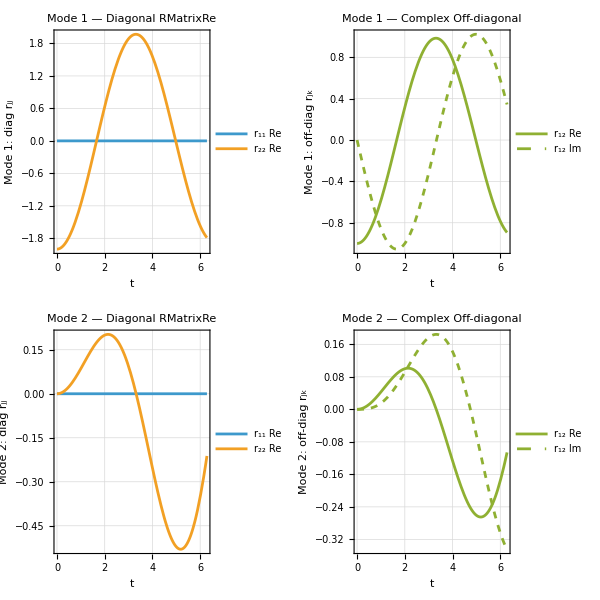

```mathematica
PlotRMatrixEvolution[EvolvedState,τ,{0,2π},{Δx->2,s1->1,s2->1,g->0.1},Nqubits,nmodes]
```

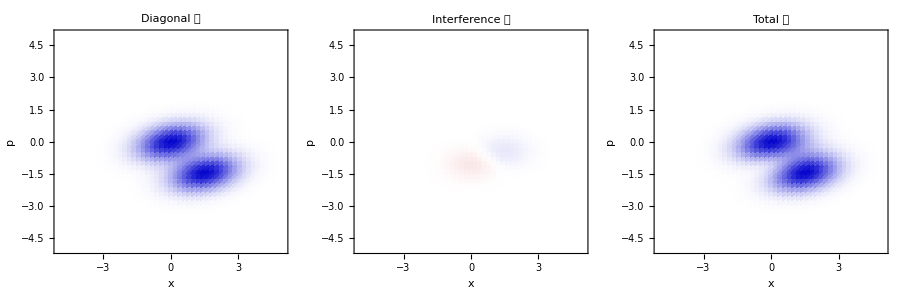
-Graphics--Graphics-

```mathematica
PlotWignerFunction[FinalState,{Δx->5,s1->1,s2->2,g->0.3,τ->π}, 2,(*modeChosen*){-5,5},(*xRange*){-5,5},(*pRange*)300         (*plotSize*)]
```